# Cardioband TR Synthetic Patient-Level Demo

## This notebook creates simulated patient-level data constrained to the aggregate outcomes in Gray WA et al. It is for demo and teaching only; these are not real trial records.

## Load package

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{NotebookDirectory[], "src", "CardiobandTRModel.wl"}]];
```

## Generate synthetic data

```mathematica
SeedRandom[42];
data = CardiobandTRModel`SimulatePatientDataset[42];
Dataset[data]
```

## Synthetic summary versus aggregate paper targets

```mathematica
summary = CardiobandTRModel`SummarizeSimulatedDataset[data];
Dataset[summary]
```

## TR grade shift

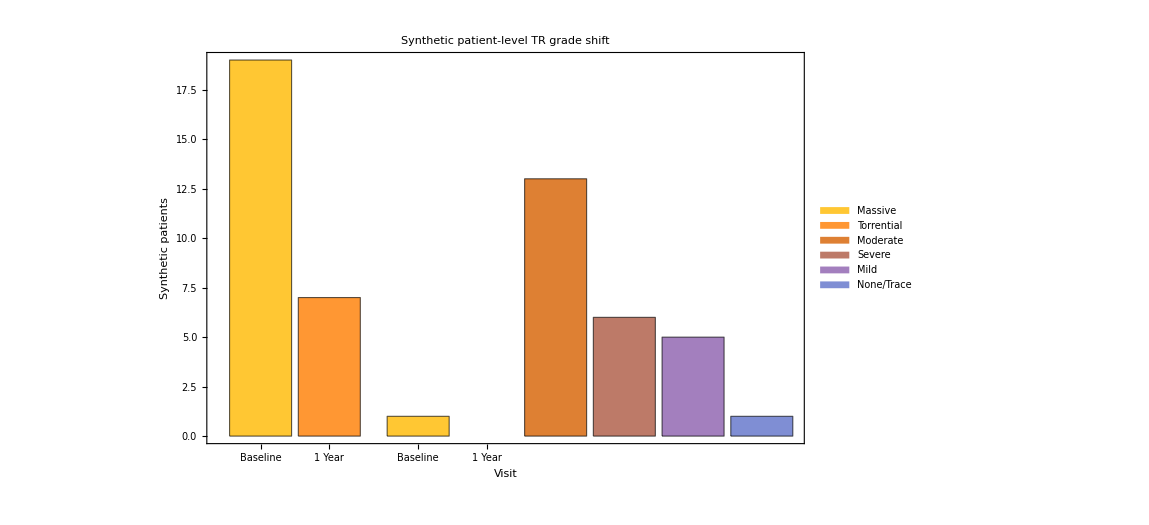

```mathematica
follow = Select[data, TrueQ[#HasOneYearEcho] &];
BarChart[{Counts[follow[[All, "TRGradeBaseline"]]], Counts[follow[[All, "TRGradeOneYear"]]]}, ChartLabels -> {"Baseline", "1 Year"}, ChartLegends -> Automatic, Frame -> True, FrameLabel -> {"Visit", "Synthetic patients"}, PlotLabel -> "Synthetic patient-level TR grade shift", ImageSize -> 850]
```

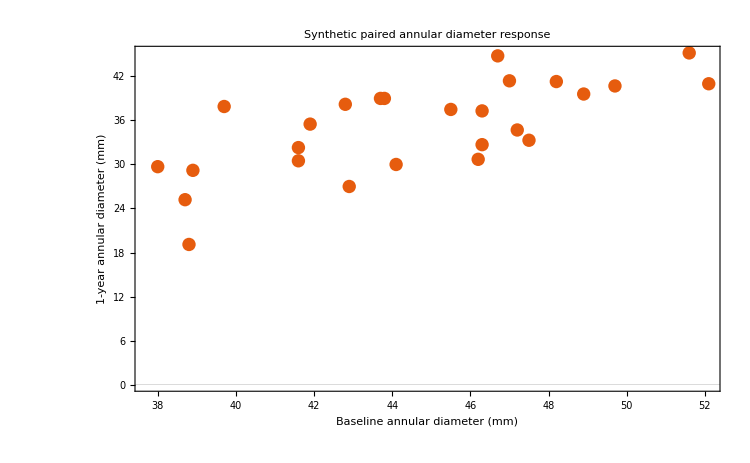

```mathematica
ListPlot[follow[[All, {"AnnularDiameterBaselineMm", "AnnularDiameterOneYearMm"}]], Frame -> True, FrameLabel -> {"Baseline annular diameter (mm)", "1-year annular diameter (mm)"}, PlotLabel -> "Synthetic paired annular diameter response", PlotTheme -> "Scientific", ImageSize -> 750]
```

## KCCQ response

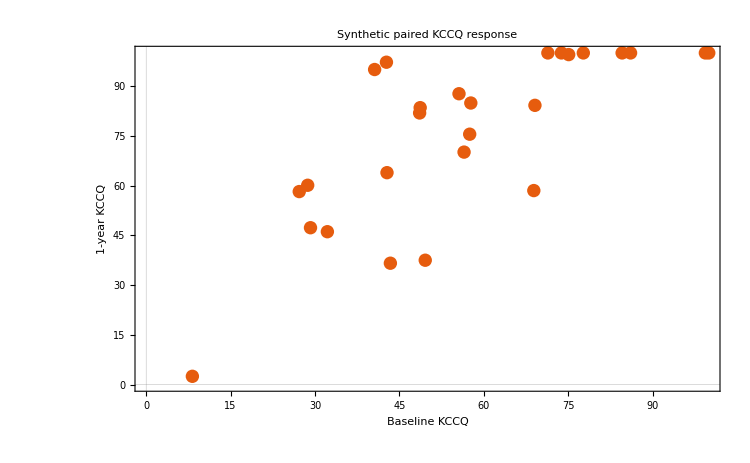

```mathematica
ListPlot[follow[[All, {"KCCQBaseline", "KCCQOneYear"}]], Frame -> True, FrameLabel -> {"Baseline KCCQ", "1-year KCCQ"}, PlotLabel -> "Synthetic paired KCCQ response", PlotTheme -> "Scientific", ImageSize -> 750]
```

## Interactive what-if: scale KCCQ treatment effect

```mathematica
Manipulate[Module[{localData, localFollow, adjusted}, localData = CardiobandTRModel`SimulatePatientDataset[42]; localFollow = Select[localData, TrueQ[#HasOneYearEcho] &]; adjusted = Map[<|#, "AdjustedKCCQOneYear" -> Min[100, #["KCCQBaseline"] + effectScale (#["KCCQOneYear"] - #["KCCQBaseline"])]|> &, localFollow]; ListPlot[adjusted[[All, {"KCCQBaseline", "AdjustedKCCQOneYear"}]], Frame -> True, FrameLabel -> {"Baseline KCCQ", "Adjusted 1-year KCCQ"}, PlotRange -> {{0, 100}, {0, 100}}, PlotLabel -> "What-if KCCQ response scale = " <> ToString[effectScale], ImageSize -> 700]], {{effectScale, 1.0, "effect scale"}, 0.25, 1.75, 0.25}]
```

## Export synthetic demo artifacts

```mathematica
CardiobandTRModel`ExportSimulationArtifacts[FileNameJoin[{NotebookDirectory[], "exports"}], 42]
```

<|Rows→37,SyntheticWarning→These rows are simulated for demonstration only and are not real Cardioband patient-level trial data.,FollowUpRows→26,TRAtMostModerate1YPercent→73.1,TRAtLeastTwoGradeReductionPercent→73.1,MeanAnnularReductionPercent→21.3,KCCQMeanChange→19.,SixMinuteWalkMeanChangeM→7.2,AllCauseDeathPercent→13.5,CardiovascularDeathPercent→8.1,HeartFailureHospitalizationPercent→10.8,SevereBleedingPercent→35.1|>

## Demo note

```mathematica
"IMPORTANT: synthetic_patient_data.csv is simulated from aggregate targets. It is useful for demos, UI prototypes, and teaching, but it is not recovered patient-level evidence."
```

IMPORTANT: synthetic_patient_data.csv is simulated from aggregate targets. It is useful for demos, UI prototypes, and teaching, but it is not recovered patient-level evidence.